# Investigating Pattern Periods in the Diagonals of the Rule 45 Cellular Automaton

Aniruddh Sriram

Mentor: Nikki Sigurdson

## Project Title & Description

#### Analyzing Diagonal Patterns in the Rule 45 Cellular Automaton

In this investigation, we examine the repetitive character of diagonal cells in the rule 45 elementary cellular automaton. It is clear that along the left edge of the automaton, a pattern exists as the cells progress diagonally downward. By moving further to the right and studying subsequent diagonals, the patterns detected exhibit increasing periods. This phenomenon is seen in the rule 30 cellular automaton as periods appear to generally increase exponentially with increasing depth. This period doubling is truly an interesting occurrence, and we study the existence of similar repetitive behavior in rule 45. To analyze the patterns for especially longer sequences of cells, we devised an efficient algorithm for detecting patterns and their periods in the diagonals. After extracting long sequences of diagonal cells with increasing depth, we employ an algorithmic approach to evaluate the changes in period and examine this data to detect order in the increasing pattern periods.

This is the rule icon for rule 45. Each neighborhood configuration is mapped to a black/white cell for the next generation.

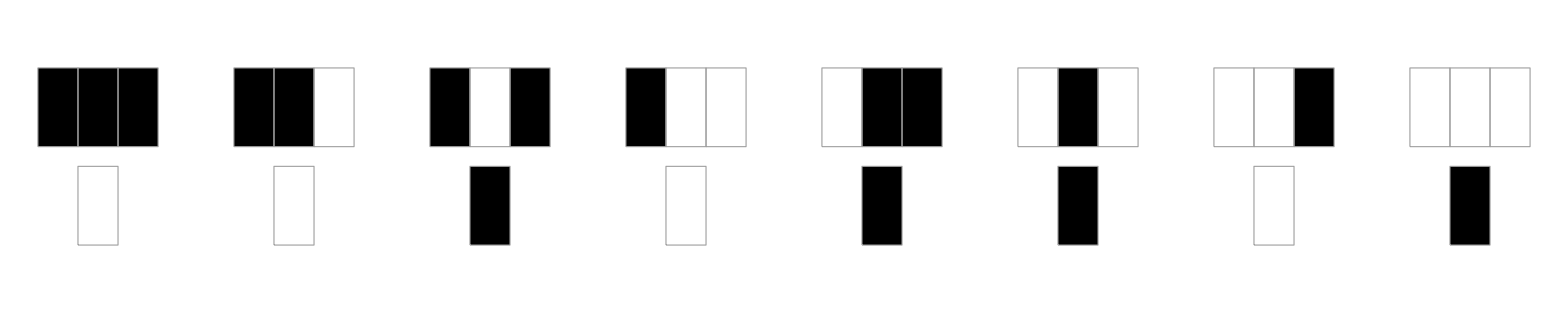

```mathematica
RulePlot[CellularAutomaton[45]]
```

Below is a visual representation of the first 100 generations of the rule 45 automaton (given initial conditions of one black cell in a background of white cells):

```mathematica
ArrayPlot[CellularAutomaton[45,{{1},0},1000]]
```

-Graphics-

Closeup of the first 20 generations. Notice the first diagonal of slope 2 along the left side, exactly along to the right side of the red arrow.

```mathematica
ArrayPlot[CellularAutomaton[45,{{1},0},20],Mesh->All, Epilog->{Red,Thickness[0.01],Arrow[{{10,21},{0,1}}]}]
```

-Graphics-

## 1. Initialize Cellular Automaton

The first step is to set up our cellular automaton. We can use the function CellularAutomaton to generate the rule 45 elementary cellular automaton. The function returns an array of 1s and 0s denoting black & white cells in the automaton. We will generate a large number of generations for our CA and initialize our search space. It is important to make these values large enough to detect longer patterns as the data tends to get more chaotic and expansive as you go further into the automaton.

### 1.1 - Access Data From Automaton

Below is an array representation of the automaton, which we can use to extract sequences of 1s and 0s to analyze patterns:

```mathematica
Grid[CellularAutomaton[45,{{1},0},20]]
```

0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1
0 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 1
0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 1
1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1

Using the function CellularAutomaton, we can treat the automaton as an array of 1s and 0s (denoting black and white cells). This makes it easy to access rows and elements at any position in the automaton. The code below retrieves the third generation of our automaton.

```mathematica
CellularAutomaton[45,{{1},0},20][[3]]
```

{0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

### 1.2 - Cellular Automata Initialization

numgen - the number of generations to produce in our automaton.

```mathematica
numgen = 30000;
```

ca - the cellular automaton array.

```mathematica
ca = CellularAutomaton[45,{{1},0},numgen];
```

ndiagonal - number of cells to analyze per diagonal.

```mathematica
ndiagonal = 24000;
```

## 2. Generating Pattern Data for a Diagonal

After initializing our cellular automaton, we need to extract data from it to conduct our analysis. Here, diagonals of slope 2 are retrieved from the left-hand edge of the automaton. From the left edge, we must move deeper into the automaton and retrieve the periodicity of the patterns generated at each depth. Here, we will first examine the process of extracting a diagonal, detecting repeating patterns using FindTransientRepeat, and finally define a useful function which can give us the pattern period of a diagonal at any given depth.

### 2.1 - Extracting Diagonals

diagnumber - the nth diagonal or number of diagonal.

```mathematica
diagnumber = 3;
```

initpos - position of initial/starting cell of diagonal.

```mathematica
initpos = Round[numgen/2]+1;
```

tbl - a 1 dimensional list of cells extracted from the nth diagonal. This is formed by traversing through the automaton in a diagonal fashion (shifting one step down and one step diagonally to the left, effectively traversing a diagonal of “slope” 2).

```mathematica
tbl = Table[ca[[x+diagnumber-1]][[initpos+diagnumber-1-Ceiling[x/2]+1]],{x,1,ndiagonal}]
```

{1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,14708,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1}
 |  |  |  |

In the automaton diagram below, the red X’s denote the cells which will be included as part of a diagonal (in the below image, the first diagonal). Each diagonal is comprised by moving two cells down, and one cell diagonally to the left. This is important because the way we process our diagonals can change the values of our periodicities.

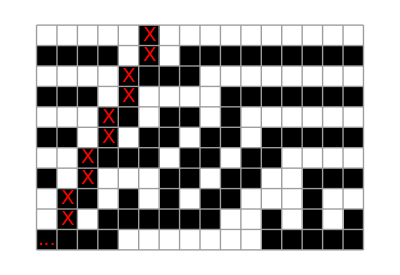

### 2.2 - Detect Repeating Patterns within Diagonal

repseq - The function FindTransientRepeat identifies a repeating sequence in tbl that occurs at least 2 times after the transient set of list elements. The repeating sequence is stored in repseq. Some diagonals had some disorder at the beginning, and a repetitive structure (the pattern) only developed later on, so FindTransientRepeat was necessary to eliminate data that obstructed our pattern.

```mathematica
repseq =FindTransientRepeat[tbl,2][[2]]
```

{1,0,1,1}

period - length of the repeating sequence as identified by FindTransientRepeat.

```mathematica
period = Length[repseq]
```

4

### 2.3 - Wrapping The Process in a Function (DiagonalPatternPeriod)

DiagonalPatternPeriod is a function that takes the parameter diagnumber (number/depth of diagonal)
and returns an integer value representing the period of the pattern present in the diagonal.

```mathematica
DiagonalPatternPeriod[diagnumber_]:=Length[FindTransientRepeat[Table[ca[[x+diagnumber-1]][[initpos+diagnumber-1-Ceiling[x/2]+1]],{x,1,ndiagonal}],2][[2]]]
```

```mathematica
DiagonalPatternPeriod[34]
```

16

## 3. Generating Pattern Data for a Range of Diagonals

Next, we attempt to generate pattern period data for diagonals of number/depth 1...n. This way, we can examine how the periods of patterns change through each step deeper into the automaton. We explore two approaches for generating this table of period values of diagonals from 1...n. The first approach is quite naive and ends up becoming very slow for larger values of n. The second approach, however, uses a search algorithm to identify breakpoints in the data without actually generating the whole list. Based on a modified binary search,  the second approach is far more efficient for larger values of n; therefore, we can delve deeper into the automaton and compute pattern periods more efficiently. However, while this algorithm is faster, it does not affect space complexity.

### 3.1 - Generate Table of Pattern Periods in Diagonals | O(m*n) Naive Approach

prdlist is a function that takes an argument n, and it returns a table of periods in diagonals 1...n. This function calls DiagonalPatternPeriod for every diagnumber (diagonal depth) value from 1...n. The time complexity of this algorithm is O(m*n), as DiagonalPatternPeriod (which is about O(m) for a diagonal of length m) is called n times.

```mathematica
prdlist[n_] := Table[DiagonalPatternPeriod[d],{d,1,n,1}]
```

```mathematica
prdlist[100]
```

{1,4,4,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,16,16,16,16,16,16,16,16,16,16,16,16,32,32,32,32,32,32,32,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96}

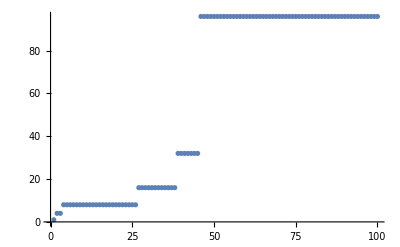

```mathematica
ListPlot[{1,4,4,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,16,16,16,16,16,16,16,16,16,16,16,16,32,32,32,32,32,32,32,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96}]
```

### 3.2 - Generate Table of Pattern Periods of Diagonals | O(m*Log(n)) Devised Algorithm (based on Binary Search)

As in section 3.1, n denotes the number of diagonals to be assessed. For n = 200, the algorithm will return a list of 200 elements containing pattern data for diagonals of depth 1...200.

```mathematica
n = 4000;
```

BreakpointSearch is a function that finds the bounds of the leftmost stretch of one unique element in the interval st...end. Modeled off a binary search, the function can identify breakpoints in approximately log(n) comparisons, which is more efficient in terms of time than the naive approach.

```mathematica
BreakpointSearch[st_,stval_,end_,endval_,f_]:=  If[stval==endval,{end+1,-1},If[st == end-1,{st+1,f[st+1]},With[{mid=Floor[(st+end)/2],midval=f[Floor[(st+end)/2]]},If[ endval==midval,BreakpointSearch[st,stval,mid,midval,f],If[stval==midval,BreakpointSearch[mid,midval,end,endval,f],BreakpointSearch[st,stval,mid,midval,f]]]]]]
```

bpoints - list of breakpoints denoting stretches of constant numerical data.

```mathematica
bpoints = {{1,DiagonalPatternPeriod[1]}};
```

```mathematica
temp =  DiagonalPatternPeriod[n];
```

The loop below calls the BreakpointSearch function to compute breakpoints and append them to bpoints. Although the loop is running the binary search based algorithms multiple times (once for each stretch of values), the periodicity of the patterns changes very slowly as you delve deeper into the automaton from the left edge, leading to long stretches of the same value. In other words,  there are not too many stretches in the data of distinct values in relation to the amount of elements we are considering. Therefore, this factor can be deemed negligible as it doesn’t greatly affect the time complexity.

```mathematica
While[Last[bpoints][[1]]≠n+1,AppendTo[bpoints,BreakpointSearch[Last[bpoints][[1]],DiagonalPatternPeriod[Last[bpoints][[1]]],n,temp,DiagonalPatternPeriod]]]
```

condensedprddata - a neat representation of diagonal periods from 1...n. 

The list contains breakpoints in the form of two element lists {{a1,b1},{a2,b2}...} where in {a,b}
	a: number of times b occurs
	b: value of the period for that set of consecutive diagonals

Note: condensedprddata is structured to display all breakpoints and pattern periods in the order they occur (traversing from diagonal 1...n)

```mathematica
condensedprddata = Table[{bpoints[[x]][[1]]-bpoints[[x-1]][[1]],bpoints[[x-1]][[2]]},{x,2,Length[bpoints]}]
```

{{1,1},{2,4},{23,8},{12,16},{7,32},{2106,96},{1849,192}}

## 4. Visualizing & Analyzing the Pattern Periodicity Data

### 4.1 - Visualizing Diagonals and Pattern Data

The following three program statements generate a visualization of how patterns are processed as diagonals are swept from the left edge. Set the number of generations by updating the variable numgenvisual. Then, run the three statements (which have already been grouped together) to produce the visualization.

Use the sliders to explore the automaton. The first slider controls the variable diagnumber, which corresponds to which diagonal you choose to process. Increasing this slider will sweep the highlighted diagonal deeper and towards the right into the automaton. The other sliders are used to pan and zoom.

When a given diagonal is highlighted, red cells denote the white cells in the automaton, and blue cells denote the black cells in the automaton. Observe the rate, increments, and regions of the automaton in which there exist changes in periodicity.

```mathematica
numgenvisual = 500;
```

```mathematica
cavisual = CellularAutomaton[45,{{1},0},numgenvisual];
```

```mathematica
Manipulate[Module[{cap0=cavisual},
xpt = FindTransientRepeat[Table[cavisual[[x+dn-1]][[Round[numgenvisual/2]+1+dn-1-Ceiling[x/2]+1]],{x,1,numgenvisual-dn+2}],2][[2]];
Table[If[cap0[[x+dn-1]][[Round[numgenvisual/2]+1+dn-1-Ceiling[x/2]+1]]== 1, cap0[[x+dn-1]][[Round[numgenvisual/2]+1+dn-1-Ceiling[x/2]+1]] = 2, cap0[[x+dn-1]][[Round[numgenvisual/2]+1+dn-1-Ceiling[x/2]+1]] =3]; ,{x,1,numgenvisual-dn+2}];
Column[{Row[xpt/. {1->Red,0->Blue}], Style["Periodicity: " <> ToString[Length[xpt]],20],ArrayPlot[cap0,ColorRules->{0->White,1->Black,2->Blue,3->Red},PlotRange->{{numgenvisual*zoom+ypos,numgenvisual*(1-zoom)+ypos},{numgenvisual*zoom+xpos,numgenvisual*(1-zoom)+xpos}},ImageSize->Large,Frame->False]}]],{{dn, 1, "Depth (diagnumber)"},1,Round[numgenvisual*0.15],1,Appearance-> "Open"},{{zoom,0.1,"Zoom"},0.1,0.49,0.01},{{xpos,0,"Pan X"},-numgenvisual*zoom+1,numgenvisual*zoom-1,1},{{ypos,0,"Pan Y"},-numgenvisual*zoom+1,numgenvisual*zoom-1,1},AppearanceElements->"SnapshotButton",FrameLabel->{{None,None},{None,Style["Visualization of Pattern Periodicity in Rule 45 Elementary CA",Red,20,Bold,Italic]}}]
```

### 4.2 - Export GIF

Following statements simply generate a GIF animation of sweeping diagonal.

```mathematica
numgengif = 200;
```

```mathematica
cagif = CellularAutomaton[45,{{1},0},numgengif];
```

```mathematica
Export[NotebookDirectory[]<>"filename.gif",Table[Module[{cap0=cagif},
xpt = FindTransientRepeat[Table[cagif[[x+dn-1]][[Round[numgengif/2]+1+dn-1-Ceiling[x/2]+1]],{x,1,numgengif-dn+2}],2][[2]];
Table[If[cap0[[x+dn-1]][[Round[numgengif/2]+1+dn-1-Ceiling[x/2]+1]]== 1, cap0[[x+dn-1]][[Round[numgengif/2]+1+dn-1-Ceiling[x/2]+1]] = 2, cap0[[x+dn-1]][[Round[numgengif/2]+1+dn-1-Ceiling[x/2]+1]] =3]; ,{x,1,numgengif-dn+2}];
Column[{ArrayPlot[cap0,ColorRules->{0->White,1->Black,2->Blue,3->Red},PlotRange->{{numgengif*0.2,numgengif*0.7},{numgengif*0.2,numgengif*0.7}},ImageSize->Full],ArrayPlot[{xpt},Mesh->All,ColorRules->{0->Red,1->Blue},ImageSize->1->30],  Style["Periodicity: " <> ToString[Length[xpt]],50]}]],{dn,1,Round[numgengif*0.2],1}], "AnimationRepetitions"-> Infinity]
```

### 4.3 - Checking for Patterns and Patterns in Periodicity of Neighborhoods of Cells in Diagonal

This is essentially the same as the DiagonalPatternPeriod function, except it generates a list of lists of three values from the previous generation (i.e. the neighbors).

```mathematica
ngen2 = 500;
```

```mathematica
ca2 = CellularAutomaton[45,{{1},0},ngen2];
```

```mathematica
DiagonalNeighborhoodPatternPeriod[diagnumber_]:=Table[{ca2[[x+diagnumber-1-1]][[Round[ngen2/2]+1+diagnumber-1-Ceiling[x/2]+1-1]],ca2[[x+diagnumber-1-1]][[Round[ngen2/2]+1+diagnumber-1-Ceiling[x/2]+1]],ca2[[x+diagnumber-1-1]][[Round[ngen2/2]+1+diagnumber-1-Ceiling[x/2]+1+1]]},{x,2,ngen2-diagnumber}]
```

As before, run FindTransientRepeat on the data (except now for neighborhoods).

```mathematica
FindTransientRepeat[DiagonalNeighborhoodPatternPeriod[2],2][[2]]
```

{{1,0,1},{1,1,1},{1,0,0},{1,1,0}}

Periodicity of cell neighborhoods for a set of diagonals:

{2,4,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,16,16,16,16,16,16,16,16,16,16,16,16,32,32,32,32,32,32,96,96,96,96,96,96}

Periodicity of cells for a set of diagonals:

{1,4,4,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,16,16,16,16,16,16,16,16,16,16,16,16,32,32,32,32,32,32,32,96,96,96,96,96}

As seen in the data above, the neighborhoods exhibit very similar periodicity as the cells themselves for each diagonal. This makes sense because the cells that make up the neighborhoods are part of diagonals that have patterns, or repetitive structure. However, as seen in the data, there are a few discontinuities at the 45th (data has 32 & 96), 1st, and 3rd  elements.